# MATH299M/CMSC389W - Visualization through Mathematica Week 7: Plotting II: RegionPlot, ContourPlot and DensityPlot

This week we start diving in to the more sophisticated plotting functions, powerful weapons in your visualization toolkit.

RegionPlot

RegionPlot highlights on the xy-plane just the points that you want. It takes three arguments, the first is a logical predicate in terms of two variables, something that will evaluate to True or False for each point in the plane, and then the next two arguments are domain tuples for those two variables, like the second argument of Plot. After that you can specify Options just like with Plot. RegionPlot works by sampling points in the plane, which can make it slow for complicated calculations, and often times it’s not very smooth when combined with Manipulate. We’ll learn a way to handle this later with Precalculation. You can use the PlotPoints option to specify the fineness of the grid used for the sampling - if your code is running slowly you can make this number smaller, or if you want a high resolution model you can make this number bigger.

Starting simple, here’s the region above the line y = x:

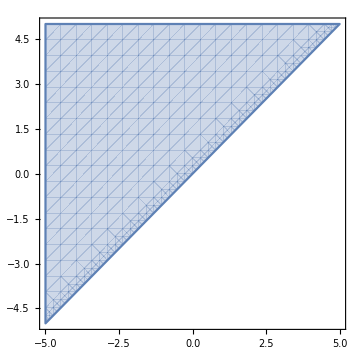

```mathematica
RegionPlot[y>x,{x,-5,5},{y,-5,5},ImageSize->Medium]
```

And here’s all points at most 1 from the origin *cough* the unit circle *cough* (and I changed the color):

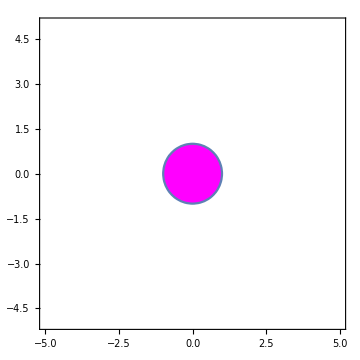

```mathematica
RegionPlot[Sqrt[x^2+y^2]≤1,{x,-5,5},{y,-5,5},ImageSize->Medium,PlotStyle->Magenta]
```

How about multiple regions, note it automatically colors them for us:

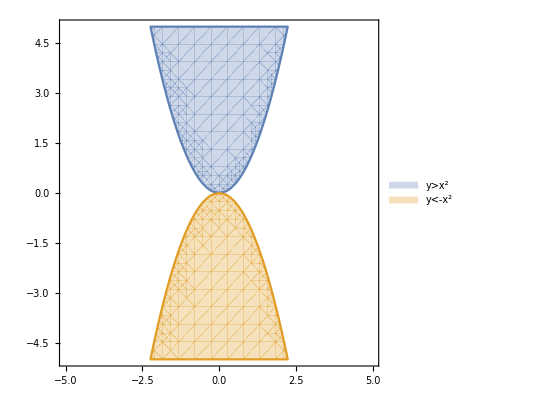

```mathematica
RegionPlot[{y>x^2,y<-x^2},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"]
```

The shading can also overlap:

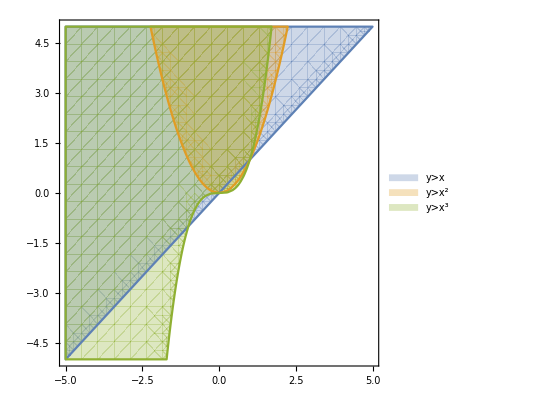

```mathematica
RegionPlot[{y>x,y>x^2,y>x^3},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"]
```

Okay, let’s do something interesting now. Let’s make a function that take the product of x and y, rounds down, and then returns whether it’s a prime. That’ll have intuitive meaning, maybe, let’s see:

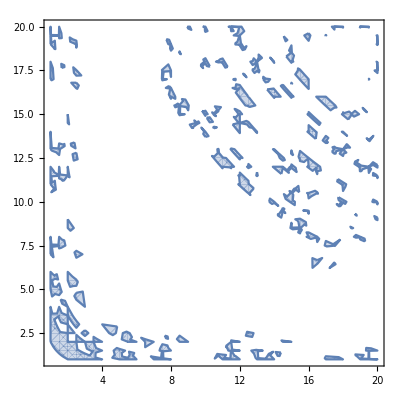

```mathematica
RegionPlot[{PrimeQ[Floor[x y]]},{x,1,20},{y,1,20}]
```

Less than clear what’s going on! And seems quite jagged. Let’s increase the PlotPoints and see if we can’t get a sensible image out of this.

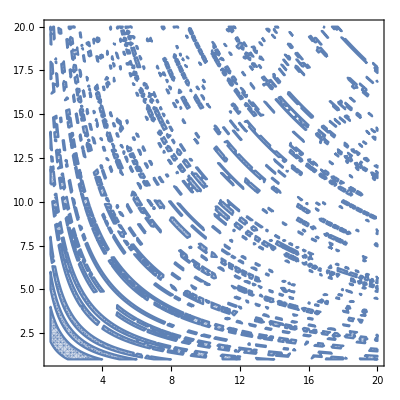

```mathematica
RegionPlot[{PrimeQ[Floor[x y]]},{x,1,20},{y,1,20},PlotPoints->50]
```

I have no idea what that means - but it’s super cool.

Okay, one more cool example, this one will use a logically complicated predicate. Don’t be scared of the x+ⅈy; if you haven’t seen a whole lot of complex analysis before, all you need to know here is that Sqrt[x^2+y^2] = Norm[x + ⅈy].

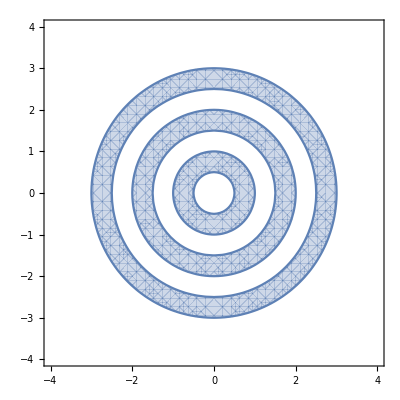

```mathematica
RegionPlot[(Norm[x+ⅈ y]>.5&&Norm[x+ⅈ y]<1)||(Norm[x+ⅈ y]>1.5&&Norm[x+ⅈ y]<2)||(Norm[x+ⅈ y]>2.5&&Norm[x+ⅈ y]<3),{x,-4,4},{y,-4,4}]
```

ContourPlot

ContourPlot is for drawing level sets of surfaces. If you haven’t taken multivariate calculus yet then you probably don’t know what this means, but we can explain. A surface is a function of two variables plotted in 3-space, that is, it’s a function f(x,y) that takes in an x value and a y value and spits out a number. You can think of this as a surface because if you have a 3d space with an x, y and z axis, and you plot the number f(x,y) on the z-axis for each x-y point, and the function is continuous, you get a smooth connected sheet floating above the xy plane (and, of course, passing below it whenever f is negative). Now, what if we take a plane parallel to the xy plane, so some function z = c where c is a constant, and plot where our surface intersects it? That’s exactly what a level set is. In general, the c level set of a function f(x,y) is the solution set to the equation f(x,y) = c, it’s all point (x,y) in the plane that map up to the value c on the surface. You should think of it as horizontal slices of the surface. ContourPlot takes three arguments - the first is an equation of the form f(x,y) = c, and the next two are domain tuples for the x and y variables, which, of course, can be any names you want besides “x” and “y”. ContourPlot also has our normal plot Options.

Horizontal slices of a cone should be easy to imagine, they’d be circles, so let’s start with that. An equation for a cone is f(x,y) = Sqrt[x^2+y^2]. If we take the level set c=2, then we’ll get the set of points in the xy plane for which Sqrt[x^2+y^2] = c, which is all points that are c from the origin, which is exactly the equation of a circle with radius c!

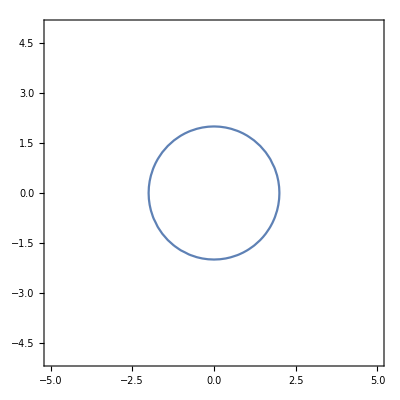

```mathematica
ContourPlot[Sqrt[x^2+y^2]==2,{x,-5,5},{y,-5,5}]
```

A pedagogical note - above the text doubled a motivation for our model and a teaching mechanism - if you haven’t seen level sets before then I’m sure you get the idea of them now, and even if you have seen them before you might already be getting a better grasp of them. This shows off just how suited Mathematica is for the classroom. It would be in-arguably useful to have this kind of tool when you’re trying to teach or learn multivariate calculus.

Okay, let’s do something more interesting now. Let’s plot a hyperboloid, which is a surface built up from hyperbolas (as you can guess by the fact that it’s function is f(x,y) = x^2-y^2, for which every level set is a hyperbola!):

```mathematica
Manipulate[ContourPlot[x^2-y^2==c,{x,-5,5},{y,-5,5},PlotPoints->40],{c,-5,5}]
```

And let' s plot a bunch of them at once because it’ll look cool:

```mathematica
Manipulate[ContourPlot[{x^2-y^2==-3c,x^2-y^2==-2c,x^2-y^2==c,x^2-y^2==c/2,x^2-y^2==c/3},{x,-5,5},{y,-5,5},PlotPoints->30],{c,-5,5}]
```

Okay, so, I mislead you a bit here. I sold ContourPlot to you as a tool from drawing level curves, which it is, but it can do more. If for the first argument instead of giving it an equation, we just give it an expression, that is, a function in terms of the two domain variables, then it’ll create a plot with colors that denote different value ranges of the surface, essentially a visualization of plotting all of the level curves at once. You can control the number of contours with Contours and then → followed by any number you want. One other fun Options is ColorFunction, which you set as a preset like “Rainbow”, or to a helper function you define, which should be a function of one variable that returns a color, in general you can use the RGBColor[·,·,·] function; it will feed the value of the first argument of ContourPlot into it for each x and y.

Cone

```mathematica
RedToBlue[val_]:=RGBColor[val,0,1/val];
GraphicsGrid[{{ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,ImageSize->300],ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->10,ColorFunction->RedToBlue,ImageSize->300],
ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->40,ColorFunction->"TemperatureMap",ImageSize->300]}},ImageSize->1200]
```

-Graphics-

Hyperbolic paraboloid/ saddle function/ Pringle’s chip

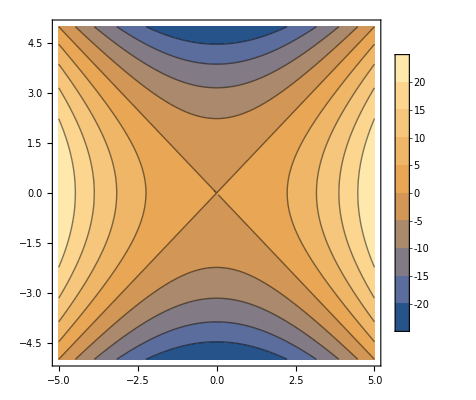

```mathematica
ContourPlot[x^2-y^2,{x,-5,5},{y,-5,5},PlotLegends->Automatic,PlotPoints->50]
```

Okay this next one is going to be ridiculously cool if you understand the physics behind it: total energy of a simply harmonic oscillator

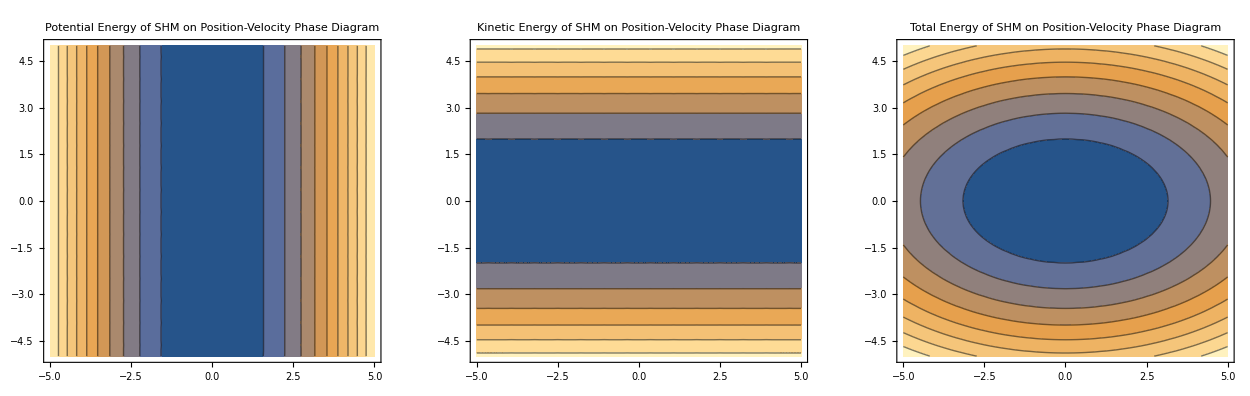

```mathematica
k=.4; (* Spring Constant *)
m=1; (* Mass *)
u[x_]:=1/2 m k x^2; (* Potential Energy of mass on spring *)
ke[x_]:=1/2 m v^2; (* Kinetic Energy of mass on spring *)
GraphicsGrid[{{ContourPlot[u[x],{x,-5,5},{v,-5,5},PlotLabel->"Potential Energy of SHM on Position-Velocity Phase Diagram"],
ContourPlot[ke[x],{x,-5,5},{v,-5,5},PlotLabel->"Kinetic Energy of SHM on Position-Velocity Phase Diagram"],
ContourPlot[ke[x]+u[x],{x,-5,5},{v,-5,5},PlotLabel->"Total Energy of SHM on Position-Velocity Phase Diagram"]}},ImageSize->1250]
```

The rightmost model shows ellipses!! That’s the shape the phase diagrams for simple harmonic oscillators look like! The x-axis is position, the y-axis is velocity, the potential energy function is the potential energy function for SHM and the kinetic energy function is the kinetic energy for SHM, which each only depend on the position and velocity respectively, and when we add those together we get the total energy of the system, which has to be constant, and so we get that an SHM with energy c is the c level set of our function!!! The shaded ellipse in the middle of the rightmost image is just because ContourPlot on a function groups together ranges of level sets, so really you can think of that ellipse as a dense stack of ellipses that shrink all the way down to the trivial ellipse, a point at the origin, a simple harmonic oscillator with 0 total energy.

DensityPlot

Now that you know ContourPlot, DensityPlot should be easy to use and understand. DensityPlot is what happens when you take the Contour Option towards infinity in CountourPlot, that is, instead of showing color coded levels of the function of two variables it shows a continuous gradient of the value. Just as ContourPlot does, it takes in three arguments, the first being a function of two variables, and the next two being domain tuples for those two variables. Normal Options apply. Below we’ll compare ContourPlot’s and DensityPlot’s of the same function.

```mathematica
GraphicsGrid[{{ContourPlot[x^2+y^2,{x,-10,10},{y,-10,10},Contours->10,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270],
ContourPlot[x^2+y^2,{x,-10,10},{y,-10,10},Contours->30,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270],DensityPlot[x^2+y^2,{x,-10,10},{y,-10,10},ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270]}},ImageSize->1100]
```

-Graphics-

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 October 8th, 2018